{a1→0.182574,b1→1.75,c1→2.63391}

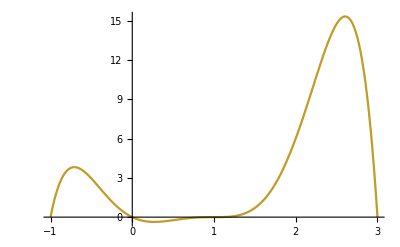

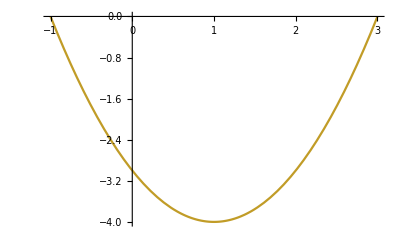

```mathematica
sol2//N
Plot[-(x+1)x(x-1)^3(x-3),{x,-1,3}]
Plot[(x+1)(x-3),{x,-1,3}]
```

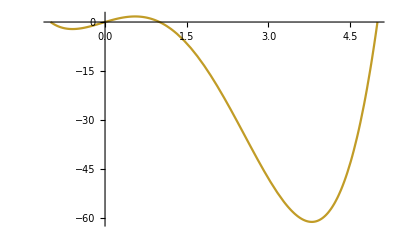

```mathematica
Plot[(x+1)x(x-1)(x-5),{x,-1,5}]
```

```mathematica
g=-(x+1)x(x-1)^3(x-3);
```

```mathematica
f=x(x-1)^3;
DorisAlgorithmCompactCase[x,f,{g}]
```

True

```mathematica
Series[1+(a1^2(x-b1)^2+c1^2)((a2^2(x-b2)^2+c2^2))(x+1)(x-3),{x,0,10}]
Series[1+(a1^2(x-b1)^2+c1^2)((a2^2(x-b2)^2+c2^2))(x+1)(x-3),{x,1,10}]
```

(1-3 (a1^2 b1^2+c1^2) (a2^2 b2^2+c2^2))+(6 a2^2 b2 (a1^2 b1^2+c1^2)+(6 a1^2 b1-2 (a1^2 b1^2+c1^2)) (a2^2 b2^2+c2^2)) x+(-3 a2^2 (a1^2 b1^2+c1^2)-2 a2^2 b2 (6 a1^2 b1-2 (a1^2 b1^2+c1^2))+(-3 a1^2+4 a1^2 b1+a1^2 b1^2+c1^2) (a2^2 b2^2+c2^2)) x^2+(-2 a2^2 b2 (-3 a1^2+4 a1^2 b1+a1^2 b1^2+c1^2)+a2^2 (6 a1^2 b1-2 (a1^2 b1^2+c1^2))+(-2 a1^2-2 a1^2 b1) (a2^2 b2^2+c2^2)) x^3+(-2 a2^2 (-2 a1^2-2 a1^2 b1) b2+a2^2 (-3 a1^2+4 a1^2 b1+a1^2 b1^2+c1^2)+a1^2 (a2^2 b2^2+c2^2)) x^4+(a2^2 (-2 a1^2-2 a1^2 b1)-2 a1^2 a2^2 b2) x^5+a1^2 a2^2 x^6+O[x]^11

(1-4 (a1^2 (-1+b1)^2+c1^2) (a2^2 (-1+b2)^2+c2^2))+(8 a2^2 (-1+b2) (a1^2 (-1+b1)^2+c1^2)+8 a1^2 (-1+b1) (a2^2 (-1+b2)^2+c2^2)) (x-1)+(-16 a1^2 a2^2 (-1+b1) (-1+b2)-4 a2^2 (a1^2 (-1+b1)^2+c1^2)+(-4 a1^2+a1^2 (-1+b1)^2+c1^2) (a2^2 (-1+b2)^2+c2^2)) (x-1)^2+(8 a1^2 a2^2 (-1+b1)-2 a2^2 (-1+b2) (-4 a1^2+a1^2 (-1+b1)^2+c1^2)-2 a1^2 (-1+b1) (a2^2 (-1+b2)^2+c2^2)) (x-1)^3+(4 a1^2 a2^2 (-1+b1) (-1+b2)+a2^2 (-4 a1^2+a1^2 (-1+b1)^2+c1^2)+a1^2 (a2^2 (-1+b2)^2+c2^2)) (x-1)^4+(-2 a1^2 a2^2 (-1+b1)-2 a1^2 a2^2 (-1+b2)) (x-1)^5+a1^2 a2^2 (x-1)^6+O[x-1]^11

```mathematica
sol1=FindInstance[(1-3 (a1^2 b1^2+c1^2) (a2^2 b2^2+c2^2))==0&&(1-4 (a1^2 (-1+b1)^2+c1^2) (a2^2 (-1+b2)^2+c2^2))==0,{a1,b1,c1,a2,b2,c2},Reals][[1]]
```

{a1→1,b1→4-2 √3,c1→0,a2→0,b2→0,c2→1/(√(-12+24 (4-2 √3)))}

```mathematica
Series[1+a1^2((x-b1)^2+c1^2)(x+1)(x-3),{x,0,10}]
Series[1+a1^2((x-b1)^2+c1^2)(x+1)(x-3),{x,1,10}]
```

(1-3 a1^2 (b1^2+c1^2))-2 (a1^2 (-3 b1+b1^2+c1^2)) x+a1^2 (-3+4 b1+b1^2+c1^2) x^2-2 (a1^2 (1+b1)) x^3+a1^2 x^4+O[x]^11

(1-4 a1^2 ((1-b1)^2+c1^2))+8 a1^2 (-1+b1) (x-1)+a1^2 (-3-2 b1+b1^2+c1^2) (x-1)^2-2 (a1^2 (-1+b1)) (x-1)^3+a1^2 (x-1)^4+O[x-1]^11

```mathematica
sol2=FindInstance[(1-3 a1^2 (b1^2+c1^2))==0&&(1-4 a1^2 ((1-b1)^2+c1^2))==0&&-1≤b1≤3,{a1,b1,c1},Reals][[1]]
```

{a1→1/(√30),b1→7/4,c1→(√111)/4}

```mathematica
s1=a1^2((x-b1)^2+c1^2)/.sol2;
F2=1+s1 (x+1)(x-3);
s0=f F2;
Reduce[s1<0,x]
Reduce[s0<0,x]
s0+s1 (g)//Simplify
```

False

False

(-1+x)^3 x